```mathematica
(*"This notebook pertains to a univariate autoregressive process. It generates artificial datasets from a known distribution, estimates parameters for each dataset, and estimates parameters for the composite of the datasets. When running you may get errors due to estimates of b with |b|≥1. Systems of this sort are unstable and the errors produced are due to trying to plot a normal distribution with negative variance!"*)
```

```mathematica
Clear["Global`*"](*Recall the usefulness of this command!*)
```

```mathematica
(*"Below is code for a command to take a list of matricies of the form {m1,m2,...}, each of which has the same number of columns, and produce a single matrix stacking m1 on top of m2 and so forth. This is needed for computing the parameter estimates for the composite system."*)
MatVec[x_]:=Module[{l,M},
l=Length[x];
M={};
For[i=1,i≤l,i++,
M=Join[M,x[[i]]]
];
M
]
```

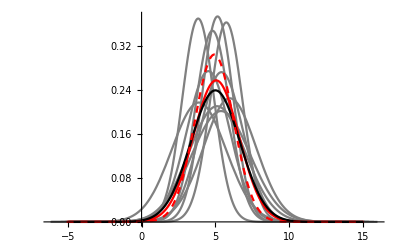

```mathematica
a=1;b=.8;(*"parameters of system. Should be regarded as nature itself, or something like that. Recall that when b is closer to 0 the system should be more stable and when closer to 1 is more unstable. Try different values! E.g., b = .2, .5, .8, .95. You can use negative values too."*)
xmean=a/(1-b);(*Theoretical mean of the system*)
xvar=1/(1-b^2);(*"Theoretical variance of the system (note: we assume the environmental noise has variance 1, i.e., is standard normal."*)

q=10;(*number of simulated datasets. Should be thought of as number of "tanks" or replicates*)
finaltime=30;(*length of each dataset*)
window=10;(*This is just a number used later for plotting*)

(*"Generate datasets. Stored as simple lists assigned to data[j] where j runs from 1 to q."*)
For[j=1,j≤q,j++,
x0=RandomVariate[NormalDistribution[xmean,Sqrt[xvar]]];(*picks a random starting value from the known distribution*)
data[j]={x0};(*defines a list with the starting value as its only member. This list will be added to over the rest of the loop*)

(*the following For loop runs the sutoregressive process, generating the data, and stores it in the jth list*)
For[i=1,i≤finaltime,i++,
x0=a+b x0+RandomVariate[NormalDistribution[]];
data[j]=Join[data[j],{x0}]]
]

(*"Estimate parameters a and b from each dataset individually."*)
For[j=1,j≤q,j++,
xmat[j]=Table[{data[j][[i]]},{i,1,finaltime}];(*species vector*)
ymat[j]=Table[{data[j][[i]]},{i,2,finaltime+1}];(*species vector shifted by one time step*)
one=Table[{1},{i,1,finaltime}];(*vector of "ones" needed for the least aquares estimate*)
zmat[j]=Transpose[Join[Transpose[one],Transpose[xmat[j]]]];(*joining the species vector with the "ones" vector*)
dmat[j]=Inverse[Transpose[zmat[j]].zmat[j]].Transpose[zmat[j]].ymat[j](*This is the linear least squares procedure that generates the estimate. The jth estimate is for the jth tank.*)
]

(*Estimate parameters a and b for the composite dataset.*)
onemore={Table[1,{i,1,q*finaltime}]};(*just a longer vector of ones*)
X=MatVec[Table[xmat[j],{j,1,q}]];(*this and the following stack the species vectors on top of each other to make one long vector*)
Y=MatVec[Table[ymat[j],{j,1,q}]];
Z=Transpose[Join[onemore,Transpose[X]]];
DD=Inverse[Transpose[Z].Z].Transpose[Z].Y;(*complete the linear least squares for the composite system*) 

(*Generate plots of the stationary distributions derived from the individual datasets (Gray).*)
For[j=1,j≤q,j++,
aest[j]=dmat[j][[1,1]];best[j]=dmat[j][[2,1]];(*dmat[j] contains both estimates of "a" and "b" for tank j. This just extracts these estimates and gives them names. These parameters determine totally the estimates stationary distributions.*)
meanest[j]=aest[j]/(1-best[j]);(*mean of the stationary dist. estimated from tank j.*)
varest[j]=1/(1-(best[j])^2);(*variance of stationary dist estimated from tank j*)
plot[j]=Plot[PDF[NormalDistribution[meanest[j],1/(Sqrt[1-(best[j])^2])],x],{x,meanest[j]-window,meanest[j]+window},PlotStyle->Gray,PlotRange->All]
]

(*Below we find estimates of paramters "a" and "b" by averging the estimated paramters from each tank*)
aavg=Mean[Table[aest[j],{j,1,q}]];
bavg=Mean[Table[best[j],{j,1,q}]];
meanavg=aavg/(1-bavg);(*the mean of the stationary dist defined by averaged paramteres*)
varavg=1/(1-bavg^2);(*variance of the stationary dist defined by the averaged parameters.*)
plotavg=Plot[PDF[NormalDistribution[meanavg,Sqrt[varavg]],x],{x,meanavg-window,meanavg+window},PlotStyle->{Red,Dashed}];

(*Generate plot of the stationary distribution derived from the composite dataset (Red).*)
acomp=DD[[1,1]];bcomp=DD[[2,1]];
meancomp=acomp/(1-bcomp);
varcomp=1/(1-(bcomp)^2);
plot[q+1]=Plot[PDF[NormalDistribution[meancomp,1/(Sqrt[1-(bcomp)^2])],x],{x,meancomp-window,meancomp+window},PlotStyle->Red];

(*Generate plot of the stationary distribution of the system itself (Black)*)
plot[0]=Plot[PDF[NormalDistribution[xmean,Sqrt[xvar]],x],{x,xmean-window,xmean+window},PlotStyle->Black];

(*Show all plots*)
plotall=Show[Table[plot[j],{j,1,q}],plot[q+1],plot[0],PlotRange->All];
Show[plotall,plotavg]
```